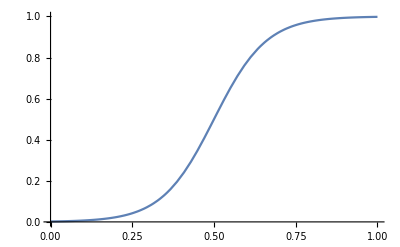

```mathematica
Plot[1/(1+Exp[-(x-.5)/.08]),{x,0,1},PlotRange->{0,1}]
```

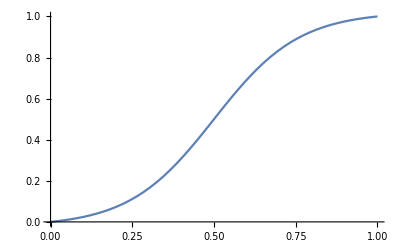

```mathematica
smoothfunc[a_,y_]:=1/(1+Exp[-(y-.5)/a]);
scaledsmoothfunc[a_,x_]:=(smoothfunc[a,x]-smoothfunc[a,0])*1/(smoothfunc[a,1]-smoothfunc[a,0]);
Plot[scaledsmoothfunc[0.13,x],{x,0,1},PlotRange->Full]
```

```mathematica
scaledsmoothfunc[a,x]//FullSimplify
```

(ⅇ^(0.5/a) (-1+ⅇ^(x/a)))/((-1+ⅇ^(0.5/a)) (ⅇ^(0.5/a)+ⅇ^(x/a)))